## Clifford tetrahedron operators(Refer to Section 3 for further details):

## Case1: A^2=B^2=1 The operators A and B can be realized by Clifford generators which are Hermitian. Then tetrahedron operators becomes R_ijk= α_1 B_iB_j B_k+ α_2 A_i A_j B_k + α_3 A_iB_jA_k + α_4B_iA_jA_k Simplest choice : A=X, B=Z;

```mathematica
Rijk:=({{ⅇ^(ⅈ θ4) r4, 0, 0, ⅇ^(ⅈ θ3) r3, 0, ⅇ^(ⅈ θ2) r2, ⅇ^(ⅈ θ1) r1, 0}, {0, -ⅇ^(ⅈ θ4) r4, ⅇ^(ⅈ θ3) r3, 0, ⅇ^(ⅈ θ2) r2, 0, 0, -ⅇ^(ⅈ θ1) r1}, {0, ⅇ^(ⅈ θ3) r3, -ⅇ^(ⅈ θ4) r4, 0, ⅇ^(ⅈ θ1) r1, 0, 0, -ⅇ^(ⅈ θ2) r2}, {ⅇ^(ⅈ θ3) r3, 0, 0, ⅇ^(ⅈ θ4) r4, 0, -ⅇ^(ⅈ θ1) r1, -ⅇ^(ⅈ θ2) r2, 0}, {0, ⅇ^(ⅈ θ2) r2, ⅇ^(ⅈ θ1) r1, 0, -ⅇ^(ⅈ θ4) r4, 0, 0, -ⅇ^(ⅈ θ3) r3}, {ⅇ^(ⅈ θ2) r2, 0, 0, -ⅇ^(ⅈ θ1) r1, 0, ⅇ^(ⅈ θ4) r4, -ⅇ^(ⅈ θ3) r3, 0}, {ⅇ^(ⅈ θ1) r1, 0, 0, -ⅇ^(ⅈ θ2) r2, 0, -ⅇ^(ⅈ θ3) r3, ⅇ^(ⅈ θ4) r4, 0}, {0, -ⅇ^(ⅈ θ1) r1, -ⅇ^(ⅈ θ2) r2, 0, -ⅇ^(ⅈ θ3) r3, 0, 0, -ⅇ^(ⅈ θ4) r4}})
```

note that $α_i=r_i Exp[I  θ_i ]$

## Unitary Solutions (case1): We have identified five unique unitary solutions:

Unimodular solutions(Refer to Table 1 in Section 3):

```mathematica
C1Rijk[1]:=({{ⅇ^(ⅈ θ3)/2, 0, 0, ⅇ^(ⅈ θ3)/2, 0, ⅇ^(ⅈ θ2)/2, ⅇ^(ⅈ θ2)/2, 0}, {0, -ⅇ^(ⅈ θ3)/2, ⅇ^(ⅈ θ3)/2, 0, ⅇ^(ⅈ θ2)/2, 0, 0, -ⅇ^(ⅈ θ2)/2}, {0, ⅇ^(ⅈ θ3)/2, -ⅇ^(ⅈ θ3)/2, 0, ⅇ^(ⅈ θ2)/2, 0, 0, -ⅇ^(ⅈ θ2)/2}, {ⅇ^(ⅈ θ3)/2, 0, 0, ⅇ^(ⅈ θ3)/2, 0, -ⅇ^(ⅈ θ2)/2, -ⅇ^(ⅈ θ2)/2, 0}, {0, ⅇ^(ⅈ θ2)/2, ⅇ^(ⅈ θ2)/2, 0, -ⅇ^(ⅈ θ3)/2, 0, 0, -ⅇ^(ⅈ θ3)/2}, {ⅇ^(ⅈ θ2)/2, 0, 0, -ⅇ^(ⅈ θ2)/2, 0, ⅇ^(ⅈ θ3)/2, -ⅇ^(ⅈ θ3)/2, 0}, {ⅇ^(ⅈ θ2)/2, 0, 0, -ⅇ^(ⅈ θ2)/2, 0, -ⅇ^(ⅈ θ3)/2, ⅇ^(ⅈ θ3)/2, 0}, {0, -ⅇ^(ⅈ θ2)/2, -ⅇ^(ⅈ θ2)/2, 0, -ⅇ^(ⅈ θ3)/2, 0, 0, -ⅇ^(ⅈ θ3)/2}})
```

More Unitary solutions(Refer to Table 2 in Section 3)

```mathematica
C1Rijk[2]:=({{0.18966634804838792-0.18815295425996584 ⅈ, 0, 0, -0.02533705888476364-0.3689877110038693 ⅈ, 0, 0.08149587169065145+0.4823785855225293 ⅈ, -0.6992478151610539+0.25209732429279735 ⅈ, 0}, {0, -0.18966634804838792+0.18815295425996584 ⅈ, -0.02533705888476364-0.3689877110038693 ⅈ, 0, 0.08149587169065145+0.4823785855225293 ⅈ, 0, 0, 0.6992478151610539-0.25209732429279735 ⅈ}, {0, -0.02533705888476364-0.3689877110038693 ⅈ, -0.18966634804838792+0.18815295425996584 ⅈ, 0, -0.6992478151610539+0.25209732429279735 ⅈ, 0, 0, -0.08149587169065145-0.4823785855225293 ⅈ}, {-0.02533705888476364-0.3689877110038693 ⅈ, 0, 0, 0.18966634804838792-0.18815295425996584 ⅈ, 0, 0.6992478151610539-0.25209732429279735 ⅈ, -0.08149587169065145-0.4823785855225293 ⅈ, 0}, {0, 0.08149587169065145+0.4823785855225293 ⅈ, -0.6992478151610539+0.25209732429279735 ⅈ, 0, -0.18966634804838792+0.18815295425996584 ⅈ, 0, 0, 0.02533705888476364+0.3689877110038693 ⅈ}, {0.08149587169065145+0.4823785855225293 ⅈ, 0, 0, 0.6992478151610539-0.25209732429279735 ⅈ, 0, 0.18966634804838792-0.18815295425996584 ⅈ, 0.02533705888476364+0.3689877110038693 ⅈ, 0}, {-0.6992478151610539+0.25209732429279735 ⅈ, 0, 0, -0.08149587169065145-0.4823785855225293 ⅈ, 0, 0.02533705888476364+0.3689877110038693 ⅈ, 0.18966634804838792-0.18815295425996584 ⅈ, 0}, {0, 0.6992478151610539-0.25209732429279735 ⅈ, -0.08149587169065145-0.4823785855225293 ⅈ, 0, 0.02533705888476364+0.3689877110038693 ⅈ, 0, 0, -0.18966634804838792+0.18815295425996584 ⅈ}})
```

```mathematica
C1Rijk[2]//Eigenvalues
```

```mathematica
{0.9450729760153309-0.3268594040341034 ⅈ,-0.8327553504035546+0.553641153071423 ⅈ,0.8327553504035544-0.5536411530714234 ⅈ,-0.6164143976880813-0.7874219264935671 ⅈ,-0.9450729760153294+0.32685940403410313 ⅈ,0.6164143976880808+0.7874219264935673 ⅈ,-0.402748536537251+0.9153106665592301 ⅈ,0.40274853653725057-0.9153106665592295 ⅈ}
```

{0.945073-0.326859 ⅈ,-0.832755+0.553641 ⅈ,0.832755-0.553641 ⅈ,-0.616414-0.787422 ⅈ,-0.945073+0.326859 ⅈ,0.616414+0.787422 ⅈ,-0.402749+0.915311 ⅈ,0.402749-0.915311 ⅈ}

```mathematica
0.9450729760153309-0.3268594040341034 ⅈ
```

```mathematica
-0.9450729760153294+0.32685940403410313 ⅈ
```

0.945073-0.326859 ⅈ

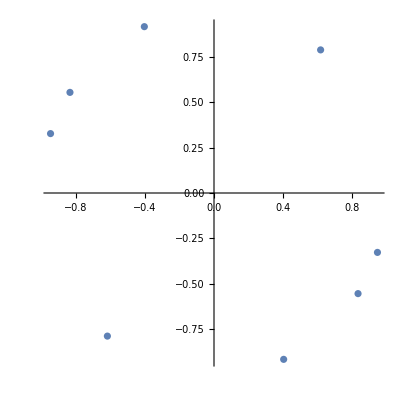

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%160,AspectRatio->1]
```

```mathematica
C1Rijk[3]:=({{ⅇ^(ⅈ (π/2+θ1)) Sin[ϕ], 0, 0, 0, 0, 0, ⅇ^(ⅈ θ1) Cos[ϕ], 0}, {0, -ⅇ^(ⅈ (π/2+θ1)) Sin[ϕ], 0, 0, 0, 0, 0, -ⅇ^(ⅈ θ1) Cos[ϕ]}, {0, 0, -ⅇ^(ⅈ (π/2+θ1)) Sin[ϕ], 0, ⅇ^(ⅈ θ1) Cos[ϕ], 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ (π/2+θ1)) Sin[ϕ], 0, -ⅇ^(ⅈ θ1) Cos[ϕ], 0, 0}, {0, 0, ⅇ^(ⅈ θ1) Cos[ϕ], 0, -ⅇ^(ⅈ (π/2+θ1)) Sin[ϕ], 0, 0, 0}, {0, 0, 0, -ⅇ^(ⅈ θ1) Cos[ϕ], 0, ⅇ^(ⅈ (π/2+θ1)) Sin[ϕ], 0, 0}, {ⅇ^(ⅈ θ1) Cos[ϕ], 0, 0, 0, 0, 0, ⅇ^(ⅈ (π/2+θ1)) Sin[ϕ], 0}, {0, -ⅇ^(ⅈ θ1) Cos[ϕ], 0, 0, 0, 0, 0, -ⅇ^(ⅈ (π/2+θ1)) Sin[ϕ]}})
```

```mathematica
C1Rijk[4]:=({{ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, 0, 0, ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, 0, ⅇ^(ⅈ θ) √(1-3 r1^2), ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, 0}, {0, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1, ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, 0, ⅇ^(ⅈ θ) √(1-3 r1^2), 0, 0, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1}, {0, ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1, 0, ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, 0, 0, -ⅇ^(ⅈ θ) √(1-3 r1^2)}, {ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, 0, 0, ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, 0, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1, -ⅇ^(ⅈ θ) √(1-3 r1^2), 0}, {0, ⅇ^(ⅈ θ) √(1-3 r1^2), ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, 0, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1, 0, 0, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1}, {ⅇ^(ⅈ θ) √(1-3 r1^2), 0, 0, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1, 0, ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1, 0}, {ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, 0, 0, -ⅇ^(ⅈ θ) √(1-3 r1^2), 0, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1, ⅇ^(ⅈ (θ-ArcCos[r1/(√(1-3 r1^2))])) r1, 0}, {0, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1, -ⅇ^(ⅈ θ) √(1-3 r1^2), 0, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1, 0, 0, ⅈ ⅇ^(ⅈ (θ+ArcSin[r1/(√(1-3 r1^2))])) r1}})
```

```mathematica
C1Rijk[5]:=({{0, 0, 0, 0, 0, -ⅈ √(1-r1^2), r1, 0}, {0, 0, 0, 0, -ⅈ √(1-r1^2), 0, 0, -r1}, {0, 0, 0, 0, r1, 0, 0, ⅈ √(1-r1^2)}, {0, 0, 0, 0, 0, -r1, ⅈ √(1-r1^2), 0}, {0, -ⅈ √(1-r1^2), r1, 0, 0, 0, 0, 0}, {-ⅈ √(1-r1^2), 0, 0, -r1, 0, 0, 0, 0}, {r1, 0, 0, ⅈ √(1-r1^2), 0, 0, 0, 0}, {0, -r1, ⅈ √(1-r1^2), 0, 0, 0, 0, 0}})
```

## Unitarity check

```mathematica
UC[i_]:=FullSimplify[C1Rijk[i].ConjugateTranspose[C1Rijk[i]]/.Conjugate[x_]->x]//Chop//N//Rationalize//MatrixForm
```

```mathematica
Table[UC[i],{i,1,5}]
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

## Case 2: A^2=A, B^2=0 ; Simplest choice: A=Z,B=X+i Y

## No Unitary Solutions for case 2

## Case 3: A^2=A, B^2=B, A.B=0=B.A ; Simplest choice: A=(1-Z)/2,B=(1+Z)/2

## Unitary Solutions (case3)

```mathematica
A[1]:=IdentityMatrix[2]
```

```mathematica
A[2]:=(IdentityMatrix[2]-PauliMatrix[3])/2
```

```mathematica
A[3]:=(IdentityMatrix[2]+PauliMatrix[3])/2
```

```mathematica
C3Rijk=Sum[Subscript[α, i,j,k] KroneckerProduct[A[i],A[j],A[k]],{i,1,3},{j,1,3},{k,1,3}]//MatrixForm
```

(α_(1,1,1)+α_(1,1,3)+α_(1,3,1)+α_(1,3,3)+α_(3,1,1)+α_(3,1,3)+α_(3,3,1)+α_(3,3,3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | α_(1,1,1)+α_(1,1,2)+α_(1,3,1)+α_(1,3,2)+α_(3,1,1)+α_(3,1,2)+α_(3,3,1)+α_(3,3,2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | α_(1,1,1)+α_(1,1,3)+α_(1,2,1)+α_(1,2,3)+α_(3,1,1)+α_(3,1,3)+α_(3,2,1)+α_(3,2,3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | α_(1,1,1)+α_(1,1,2)+α_(1,2,1)+α_(1,2,2)+α_(3,1,1)+α_(3,1,2)+α_(3,2,1)+α_(3,2,2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | α_(1,1,1)+α_(1,1,3)+α_(1,3,1)+α_(1,3,3)+α_(2,1,1)+α_(2,1,3)+α_(2,3,1)+α_(2,3,3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | α_(1,1,1)+α_(1,1,2)+α_(1,3,1)+α_(1,3,2)+α_(2,1,1)+α_(2,1,2)+α_(2,3,1)+α_(2,3,2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | α_(1,1,1)+α_(1,1,3)+α_(1,2,1)+α_(1,2,3)+α_(2,1,1)+α_(2,1,3)+α_(2,2,1)+α_(2,2,3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | α_(1,1,1)+α_(1,1,2)+α_(1,2,1)+α_(1,2,2)+α_(2,1,1)+α_(2,1,2)+α_(2,2,1)+α_(2,2,2))

Comment: for unitary, the choice of diagonal coefficients as phases yields a unitary solution.

## More Tetrahedron operators from Clifford Yang-Baxter so- lutions(see section 4.2): R_ijk=α A_i A_j C_k+β B_i B_j C_k

## case1: {A,B}={A,C}={B,C}=0, where A^2=B^2=C^2=1; A=X,B=Z,C=Y

```mathematica
RCijk:=({{0, ⅇ^(ⅈ θ) Cos[ϕ], 0, 0, 0, 0, 0, -ⅈ ⅇ^(ⅈ θ) Sin[ϕ]}, {-ⅇ^(ⅈ θ) Cos[ϕ], 0, 0, 0, 0, 0, ⅈ ⅇ^(ⅈ θ) Sin[ϕ], 0}, {0, 0, 0, -ⅇ^(ⅈ θ) Cos[ϕ], 0, -ⅈ ⅇ^(ⅈ θ) Sin[ϕ], 0, 0}, {0, 0, ⅇ^(ⅈ θ) Cos[ϕ], 0, ⅈ ⅇ^(ⅈ θ) Sin[ϕ], 0, 0, 0}, {0, 0, 0, -ⅈ ⅇ^(ⅈ θ) Sin[ϕ], 0, -ⅇ^(ⅈ θ) Cos[ϕ], 0, 0}, {0, 0, ⅈ ⅇ^(ⅈ θ) Sin[ϕ], 0, ⅇ^(ⅈ θ) Cos[ϕ], 0, 0, 0}, {0, -ⅈ ⅇ^(ⅈ θ) Sin[ϕ], 0, 0, 0, 0, 0, ⅇ^(ⅈ θ) Cos[ϕ]}, {ⅈ ⅇ^(ⅈ θ) Sin[ϕ], 0, 0, 0, 0, 0, -ⅇ^(ⅈ θ) Cos[ϕ], 0}})
```

## Unitarity check

```mathematica
U1=FullSimplify[RCijk.ConjugateTranspose[RCijk]/.Conjugate[x_]->x]//MatrixForm
```

RCijk.ConjugateTranspose[RCijk]

## Case2: {A,B}=[A,C]=[B,C]=0; A=(1+Z)/2,B=(1-Z)/2,C=Z;

```mathematica
RACijk:=({{Subscript[β, 1], 0, 0, 0, 0, 0, 0, 0}, {0, -Subscript[β, 1], 0, 0, 0, 0, 0, 0}, {0, 0, Subscript[β, 2], 0, 0, 0, 0, 0}, {0, 0, 0, -Subscript[β, 2], 0, 0, 0, 0}, {0, 0, 0, 0, Subscript[β, 3], 0, 0, 0}, {0, 0, 0, 0, 0, -Subscript[β, 3], 0, 0}, {0, 0, 0, 0, 0, 0, Subscript[β, 4], 0}, {0, 0, 0, 0, 0, 0, 0, -Subscript[β, 4]}})
```

where β_1=α_0+α_1+α_2+α_8, β_2=α_0+α_1+α_4+α_5, β_3=α_0+α_2+α_3+α_6,β_4=α_0+α_3+α_4+α_7  being phases for unitary

## **The Tetrahedron Operators Corresponding to 11 Classes of Hietarinta’s Yang-Baxter Solutions** : R_ijk=Y_ij M_k, where M satisfies [Y,M⊗ M]=0(non-invertible solutions) (*Refer to Section 4.1 for further details.*)

```mathematica
Clear[a,b,c,d,k,p,q,r,s]
```

### Class1 : M31 satisfies [Y_(H3,1),M31⊗ M31]=0

```mathematica
Subscript[Y, H3,1]:=({{k, 0, 0, 0}, {0, 0, p, 0}, {0, q, 0, 0}, {0, 0, 0, s}}); M31:=({{a, 0}, {0, d}});MM31:=KroneckerProduct[M31,M31];
MatrixForm[Subscript[Y, H3,1].MM31-MM31.Subscript[Y, H3,1]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Class2 : M21 satisfies [Y_(H2,1),M21⊗ M21]=0

```mathematica
Subscript[Y, H2,1]:=({{k^2, 0, 0, 0}, {0, k^2-p q, k p, 0}, {0, k q, 0, 0}, {0, 0, 0, k^2}}); M21:=({{a, 0}, {0, d}});MM21:=KroneckerProduct[M21,M21];
MatrixForm[Subscript[Y, H2,1].MM21-MM21.Subscript[Y, H2,1]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Class3 : M22 satisfies [Y_(H3,1),M22⊗ M22]=0

```mathematica
Subscript[Y, H2,2]:=({{k^2, 0, 0, 0}, {0, k^2-p q, k p, 0}, {0, k q, 0, 0}, {0, 0, 0, -p q}}); M22:=({{a, 0}, {0, d}});MM22:=KroneckerProduct[M22,M22];
MatrixForm[Subscript[Y, H2,2].MM22-MM22.Subscript[Y, H2,2]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Class4: M23 satisfies [Y_(H2,3),M23⊗ M23]=0

```mathematica
Subscript[Y, H2,3]:=({{k, p, q, s}, {0, 0, k, p}, {0, k, 0, q}, {0, 0, 0, k}}); Subscript[M23, 1]:=({{a, b}, {0, a}});Subscript[M23, 2]:=({{1, -(2s)/(p+q)}, {0, 1}});Subscript[MM23, 1]:=KroneckerProduct[Subscript[M23, 1],Subscript[M23, 1]];Subscript[MM23, 2]:=KroneckerProduct[Subscript[M23, 1],Subscript[M23, 1]];
Table[MatrixForm[FullSimplify[Subscript[Y, H2,3].Subscript[MM23, i]-Subscript[MM23, i].Subscript[Y, H2,3]]],{i,1,2}]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

### Class5 : M11 satisfies [Y_(H1,1),M31⊗ M31]=0

```mathematica
Subscript[Y, H1,1]:=({{p^2+2 p q-q^2, 0, 0, p^2-q^2}, {0, p^2-q^2, p^2+q^2, 0}, {0, p^2+q^2, p^2-q^2, 0}, {p^2-q^2, 0, 0, p^2-2 p q-q^2}});
 Subscript[M11, 1]:=({{1, 0}, {0, -1}});Subscript[MM11, 1]:=KroneckerProduct[Subscript[M11, 1],Subscript[M11, 1]];
Subscript[M11, 2]:=({{1, (√(p-q))/(√(p+q))}, {(√(p-q))/(√(p+q)), (p-q)/(p+q)}});Subscript[MM11, 2]:=KroneckerProduct[Subscript[M11, 2],Subscript[M11, 2]];
Subscript[M11, 3]:=({{1, -(√(p-q))/(√(p+q))}, {-(√(p-q))/(√(p+q)), (p-q)/(p+q)}});Subscript[MM11, 3]:=KroneckerProduct[Subscript[M11, 3],Subscript[M11, 3]];
Subscript[M11, 4]:=({{1, (√(p-q))/(√(p+q))}, {-(√(p-q))/(√(p+q)), (-(p-q))/(p+q)}});Subscript[MM11, 4]:=KroneckerProduct[Subscript[M11, 4],Subscript[M11, 4]];
Subscript[M11, 5]:=({{1, -(√(p-q))/(√(p+q))}, {(√(p-q))/(√(p+q)), (-(p-q))/(p+q)}});Subscript[MM11, 5]:=KroneckerProduct[Subscript[M11, 5],Subscript[M11, 5]];
Table[MatrixForm[FullSimplify[Subscript[Y, H1,1].Subscript[MM11, i]-Subscript[MM11, i].Subscript[Y, H1,1]]],{i,1,4}]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

### Class6 : M12 satisfies [Y_(H1,2),M12⊗ M12]=0

```mathematica
Subscript[Y, H1,2]:=({{p, 0, 0, k}, {0, p-q, p, 0}, {0, q, 0, 0}, {0, 0, 0, -q}});
  Subscript[M12, 1]:=({{1, 0}, {0, -1}});Subscript[MM12, 1]:=KroneckerProduct[Subscript[M12, 1],Subscript[M12, 1]];
Subscript[M12, 2]:=({{(√(p+q))/(√k), 1}, {0, 0}});Subscript[MM12, 2]:=KroneckerProduct[Subscript[M12, 2],Subscript[M12, 2]];
Subscript[M12, 3]:=({{-(√(p+q))/(√k), 1}, {0, 0}});Subscript[MM12, 3]:=KroneckerProduct[Subscript[M12, 3],Subscript[M12, 3]];
Table[MatrixForm[FullSimplify[Subscript[Y, H1,2].Subscript[MM12, i]-Subscript[MM12, i].Subscript[Y, H1,2]]],{i,1,3}]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

### Class7 : M13 satisfies [Y_(H1,3),M13⊗ M13]=0

```mathematica
Subscript[Y, H1,3]:=({{k^2, -k p, k p, p q}, {0, 0, k^2, k q}, {0, k^2, 0, -k q}, {0, 0, 0, k^2}}); M13:=({{a, b}, {0, a}});MM13:=KroneckerProduct[M13,M13];
MatrixForm[Subscript[Y, H1,3].MM13-MM13.Subscript[Y, H1,3]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Class8 : M14 satisfies [Y_(H1,4),M21⊗ M21]=0

```mathematica
Subscript[Y, H1,4]:=({{0, 0, 0, p}, {0, k, 0, 0}, {0, 0, k, 0}, {q, 0, 0, 0}}); 
Subscript[M14, 1]:=({{1, 0}, {0, -1}});Subscript[MM14, 1]:=KroneckerProduct[Subscript[M14, 1],Subscript[M14, 1]];
Subscript[M14, 2]:=({{0, 1}, {(√q)/(√p), 0}});Subscript[MM14, 2]:=KroneckerProduct[Subscript[M14, 2],Subscript[M14, 2]];
Subscript[M14, 3]:=({{0, 1}, {-(√q)/(√p), 0}});Subscript[MM14, 3]:=KroneckerProduct[Subscript[M14, 3],Subscript[M14, 3]];
Table[MatrixForm[FullSimplify[Subscript[Y, H1,4].Subscript[MM14, i]-Subscript[MM14, i].Subscript[Y, H1,4]]],{i,1,3}]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

### Class9 : M01 satisfies [Y_(H0,1),M31⊗ M31]=0

```mathematica
Subscript[Y, H0,1]:=({{1, 0, 0, 1}, {0, 0, -1, 0}, {0, -1, 0, 0}, {0, 0, 0, 1}}); M01:=({{1, 0}, {0, -1}});MM01:=KroneckerProduct[M01,M01];
MatrixForm[Subscript[Y, H0,1].MM01-MM01.Subscript[Y, H0,1]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Class10 : M02 satisfies [Y_(H0,2),M21⊗ M21]=0

```mathematica
Subscript[Y, H0,2]:=({{1, 0, 0, 1}, {0, 1, 1, 0}, {0, -1, 1, 0}, {-1, 0, 0, 1}}); M02:=({{1, 0}, {0, -1}});MM02:=KroneckerProduct[M02,M02];
MatrixForm[Subscript[Y, H0,2].MM02-MM02.Subscript[Y, H0,2]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Class11 : M23 satisfies [P_23,M23⊗ M23]=0

```mathematica
Subscript[P, 23]:=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});M23:=({{a, b}, {c, d}});MM23:=KroneckerProduct[M23,M23];
MatrixForm[Subscript[P, 23].MM23-MM23.Subscript[P, 23]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

## **The Five Families of Unitary Solutions Derived from Hietarinta’s Yang-Baxter Operators** : The unitary families: κ 𝒬 (Y ⊗ M) 𝒬^-1 and κ 𝒬 (M ⊗ Y) 𝒬^-1, where 𝒬= Q⊗Q⊗Q

## Family1: generated by the H3,1 Hietarinta class

```mathematica
Y31:=({{1, 0, 0, 0}, {0, Exp[I p], 0, 0}, {0, 0, Exp[I q], 0}, {0, 0, 0, Exp[I r]}}); M1:=({{1, 0}, {0, -1}}); Q31=({{r1 Exp[I a], r2 Exp[I b]}, {- (r1 r2)/ r3 Exp[I (a+d-b)], r3 Exp[I d]}});
```

## There are two sets of unitary tetrahedron operators

## Unitary Solution-1 : 𝒬 (Y_H31 ⊗Z)𝒬^-1

```mathematica
R31:=KroneckerProduct[Y31,M1]
𝒬31:=KroneckerProduct[Q31,Q31,Q31]
RF31:=FullSimplify[𝒬31.R31.Inverse[𝒬31],Assumptions->Element[{p,q,r,a,b,c,d,r1,r2,r3},Reals]]
RF31//MatrixForm
```

$Aborted

Unitary Condition check:

```mathematica
FullSimplify[RF31.ConjugateTranspose[RF31],Assumptions->Element[{p,q,r,a,b,c,d,r1,r2,r3},Reals]]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## Unitary Solution-2 : 𝒬 (Z ⊗ Y_H31)𝒬^-1

```mathematica
RL31:=KroneckerProduct[M1,Y31]
𝒬31:=KroneckerProduct[Q31,Q31,Q31]
RLF31:=FullSimplify[𝒬31.RL31.Inverse[𝒬31],Assumptions->Element[{p,q,r,a,b,c,d,r1,r2,r3},Reals]]
RLF31//MatrixForm
```

(-((r2-r3) (r2+r3) (ⅇ^(ⅈ r) r2^4+ⅇ^(ⅈ p) r2^2 r3^2+ⅇ^(ⅈ q) r2^2 r3^2+r3^4))/((r2^2+r3^2)^3) | (ⅇ^(ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ p) r3^2))/((r2^2+r3^2)^3) | (ⅇ^(ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ q) r3^2))/((r2^2+r3^2)^3) | (ⅇ^(2 ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2 (r2-r3) r3^2 (r2+r3))/((r2^2+r3^2)^3) | -(2 ⅇ^(ⅈ (b-d)) r2 r3 (ⅇ^(ⅈ r) r2^4+ⅇ^(ⅈ p) r2^2 r3^2+ⅇ^(ⅈ q) r2^2 r3^2+r3^4))/((r2^2+r3^2)^3) | (2 ⅇ^(2 ⅈ (b-d)) r2^2 r3^2 ((ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ p) r3^2))/((r2^2+r3^2)^3) | (2 ⅇ^(2 ⅈ (b-d)) r2^2 r3^2 ((ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ q) r3^2))/((r2^2+r3^2)^3) | (2 ⅇ^(3 ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^3 r3^3)/((r2^2+r3^2)^3)
(ⅇ^(-ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ p) r3^2))/((r2^2+r3^2)^3) | ((-r2^2+r3^2) (ⅇ^(ⅈ p) r3^4+r2^2 (ⅇ^(ⅈ q) r2^2+r3^2+ⅇ^(ⅈ r) r3^2)))/((r2^2+r3^2)^3) | ((-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2 (r2-r3) r3^2 (r2+r3))/((r2^2+r3^2)^3) | -(ⅇ^(ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((-1+ⅇ^(ⅈ q)) r2^2-(ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r3^2))/((r2^2+r3^2)^3) | (2 r2^2 r3^2 ((ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ p) r3^2))/((r2^2+r3^2)^3) | -(2 ⅇ^(ⅈ (b-d)) r2 r3 (ⅇ^(ⅈ p) r3^4+r2^2 (ⅇ^(ⅈ q) r2^2+r3^2+ⅇ^(ⅈ r) r3^2)))/((r2^2+r3^2)^3) | (2 ⅇ^(ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^3 r3^3)/((r2^2+r3^2)^3) | -(2 ⅇ^(2 ⅈ (b-d)) r2^2 r3^2 ((-1+ⅇ^(ⅈ q)) r2^2-(ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r3^2))/((r2^2+r3^2)^3)
(ⅇ^(-ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ q) r3^2))/((r2^2+r3^2)^3) | ((-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2 (r2-r3) r3^2 (r2+r3))/((r2^2+r3^2)^3) | ((-r2^2+r3^2) (ⅇ^(ⅈ q) r3^4+r2^2 (ⅇ^(ⅈ p) r2^2+r3^2+ⅇ^(ⅈ r) r3^2)))/((r2^2+r3^2)^3) | -(ⅇ^(ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((-1+ⅇ^(ⅈ p)) r2^2-(ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r3^2))/((r2^2+r3^2)^3) | (2 r2^2 r3^2 ((ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ q) r3^2))/((r2^2+r3^2)^3) | (2 ⅇ^(ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^3 r3^3)/((r2^2+r3^2)^3) | -(2 ⅇ^(ⅈ (b-d)) r2 r3 (ⅇ^(ⅈ q) r3^4+r2^2 (ⅇ^(ⅈ p) r2^2+r3^2+ⅇ^(ⅈ r) r3^2)))/((r2^2+r3^2)^3) | -(2 ⅇ^(2 ⅈ (b-d)) r2^2 r3^2 ((-1+ⅇ^(ⅈ p)) r2^2-(ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r3^2))/((r2^2+r3^2)^3)
(ⅇ^(-2 ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2 (r2-r3) r3^2 (r2+r3))/((r2^2+r3^2)^3) | -(ⅇ^(-ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((-1+ⅇ^(ⅈ q)) r2^2-(ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r3^2))/((r2^2+r3^2)^3) | -(ⅇ^(-ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((-1+ⅇ^(ⅈ p)) r2^2-(ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r3^2))/((r2^2+r3^2)^3) | ((-r2^2+r3^2) (r2^4+(ⅇ^(ⅈ p)+ⅇ^(ⅈ q)) r2^2 r3^2+ⅇ^(ⅈ r) r3^4))/((r2^2+r3^2)^3) | (2 ⅇ^(-ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^3 r3^3)/((r2^2+r3^2)^3) | (-2 (-1+ⅇ^(ⅈ q)) r2^4 r3^2+2 (ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r2^2 r3^4)/((r2^2+r3^2)^3) | (-2 (-1+ⅇ^(ⅈ p)) r2^4 r3^2+2 (ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2 r3^4)/((r2^2+r3^2)^3) | -(2 ⅇ^(ⅈ (b-d)) r2 r3 (r2^4+(ⅇ^(ⅈ p)+ⅇ^(ⅈ q)) r2^2 r3^2+ⅇ^(ⅈ r) r3^4))/((r2^2+r3^2)^3)
-(2 ⅇ^(-ⅈ (b-d)) r2 r3 (ⅇ^(ⅈ r) r2^4+ⅇ^(ⅈ p) r2^2 r3^2+ⅇ^(ⅈ q) r2^2 r3^2+r3^4))/((r2^2+r3^2)^3) | (2 r2^2 r3^2 ((ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ p) r3^2))/((r2^2+r3^2)^3) | (2 r2^2 r3^2 ((ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ q) r3^2))/((r2^2+r3^2)^3) | (2 ⅇ^(ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^3 r3^3)/((r2^2+r3^2)^3) | ((r2-r3) (r2+r3) (ⅇ^(ⅈ r) r2^4+ⅇ^(ⅈ p) r2^2 r3^2+ⅇ^(ⅈ q) r2^2 r3^2+r3^4))/((r2^2+r3^2)^3) | -(ⅇ^(ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ p) r3^2))/((r2^2+r3^2)^3) | -(ⅇ^(ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ q) r3^2))/((r2^2+r3^2)^3) | -(ⅇ^(2 ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2 (r2-r3) r3^2 (r2+r3))/((r2^2+r3^2)^3)
(2 ⅇ^(-2 ⅈ (b-d)) r2^2 r3^2 ((ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ p) r3^2))/((r2^2+r3^2)^3) | -(2 ⅇ^(-ⅈ (b-d)) r2 r3 (ⅇ^(ⅈ p) r3^4+r2^2 (ⅇ^(ⅈ q) r2^2+r3^2+ⅇ^(ⅈ r) r3^2)))/((r2^2+r3^2)^3) | (2 ⅇ^(-ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^3 r3^3)/((r2^2+r3^2)^3) | (-2 (-1+ⅇ^(ⅈ q)) r2^4 r3^2+2 (ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r2^2 r3^4)/((r2^2+r3^2)^3) | -(ⅇ^(-ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ p) r3^2))/((r2^2+r3^2)^3) | ((r2-r3) (r2+r3) (ⅇ^(ⅈ p) r3^4+r2^2 (ⅇ^(ⅈ q) r2^2+r3^2+ⅇ^(ⅈ r) r3^2)))/((r2^2+r3^2)^3) | ((-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2 r3^2 (-r2^2+r3^2))/((r2^2+r3^2)^3) | (ⅇ^(ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((-1+ⅇ^(ⅈ q)) r2^2-(ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r3^2))/((r2^2+r3^2)^3)
(2 ⅇ^(-2 ⅈ (b-d)) r2^2 r3^2 ((ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ q) r3^2))/((r2^2+r3^2)^3) | (2 ⅇ^(-ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^3 r3^3)/((r2^2+r3^2)^3) | -(2 ⅇ^(-ⅈ (b-d)) r2 r3 (ⅇ^(ⅈ q) r3^4+r2^2 (ⅇ^(ⅈ p) r2^2+r3^2+ⅇ^(ⅈ r) r3^2)))/((r2^2+r3^2)^3) | (-2 (-1+ⅇ^(ⅈ p)) r2^4 r3^2+2 (ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2 r3^4)/((r2^2+r3^2)^3) | -(ⅇ^(-ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r2^2+r3^2-ⅇ^(ⅈ q) r3^2))/((r2^2+r3^2)^3) | ((-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2 r3^2 (-r2^2+r3^2))/((r2^2+r3^2)^3) | ((r2-r3) (r2+r3) (ⅇ^(ⅈ q) r3^4+r2^2 (ⅇ^(ⅈ p) r2^2+r3^2+ⅇ^(ⅈ r) r3^2)))/((r2^2+r3^2)^3) | (ⅇ^(ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((-1+ⅇ^(ⅈ p)) r2^2-(ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r3^2))/((r2^2+r3^2)^3)
(2 ⅇ^(-3 ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^3 r3^3)/((r2^2+r3^2)^3) | (ⅇ^(-2 ⅈ (b-d)) (-2 (-1+ⅇ^(ⅈ q)) r2^4 r3^2+2 (ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r2^2 r3^4))/((r2^2+r3^2)^3) | (ⅇ^(-2 ⅈ (b-d)) (-2 (-1+ⅇ^(ⅈ p)) r2^4 r3^2+2 (ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2 r3^4))/((r2^2+r3^2)^3) | -(2 ⅇ^(-ⅈ (b-d)) r2 r3 (r2^4+(ⅇ^(ⅈ p)+ⅇ^(ⅈ q)) r2^2 r3^2+ⅇ^(ⅈ r) r3^4))/((r2^2+r3^2)^3) | (ⅇ^(-2 ⅈ (b-d)) (-1+ⅇ^(ⅈ p)+ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r2^2 r3^2 (-r2^2+r3^2))/((r2^2+r3^2)^3) | (ⅇ^(-ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((-1+ⅇ^(ⅈ q)) r2^2-(ⅇ^(ⅈ p)-ⅇ^(ⅈ r)) r3^2))/((r2^2+r3^2)^3) | (ⅇ^(-ⅈ (b-d)) r2 (r2-r3) r3 (r2+r3) ((-1+ⅇ^(ⅈ p)) r2^2-(ⅇ^(ⅈ q)-ⅇ^(ⅈ r)) r3^2))/((r2^2+r3^2)^3) | ((r2-r3) (r2+r3) (r2^4+(ⅇ^(ⅈ p)+ⅇ^(ⅈ q)) r2^2 r3^2+ⅇ^(ⅈ r) r3^4))/((r2^2+r3^2)^3))

Unitary Condition check:

```mathematica
FullSimplify[RLF31.ConjugateTranspose[RLF31],Assumptions->Element[{p,q,r,a,b,c,d,r1,r2,r3},Reals]]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## Family2: generated by the H2, 1 Hietarinta class

```mathematica
Y21:=({{1/Sqrt[2], 0, 0, 1/Sqrt[2]}, {0, 1/Sqrt[2], 1/Sqrt[2], 0}, {0, 1/Sqrt[2], -1/Sqrt[2], 0}, {-1/Sqrt[2], 0, 0, 1/Sqrt[2]}}); M2:=({{1, 0}, {0, -1}}); Q21=({{r1 Exp[I a], r2 Exp[I b]}, {- r2 Exp[I (a+d-b)], r1 Exp[I d]}});
```

## There are two sets of unitary tetrahedron operators

## Unitary Solution-1: 𝒬 (Y_H21 ⊗Z)𝒬^-1

```mathematica
R21:=KroneckerProduct[Y21,M2]
𝒬21:=KroneckerProduct[Q21,Q21,Q21]
RF21:=FullSimplify[𝒬21.R21.Inverse[𝒬21],Assumptions->Element[{r2,r1,a,b,c,d},Reals]]
RF21//MatrixForm
```

(((r1-r2) (r1+r2) ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | (ⅇ^(-2 ⅈ (a+d)) (r1-r2) (r1+r2) (ⅇ^(4 ⅈ a) r1^4-ⅇ^(4 ⅈ b) r2^4))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-ⅈ (2 a-b+3 d)) r1 r2 (-ⅇ^(4 ⅈ a) r1^4+ⅇ^(4 ⅈ b) r2^4))/((r1^2+r2^2)^3)
-(√2 ⅇ^(-ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | -((r1-r2) (r1+r2) ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 r2 (-r1^2+r2^2) (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | -(ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-ⅈ (2 a+b+d)) r1 r2 (-ⅇ^(4 ⅈ a) r1^4+ⅇ^(4 ⅈ b) r2^4))/((r1^2+r2^2)^3) | -(ⅇ^(-2 ⅈ (a+d)) (r1-r2) (r1+r2) (ⅇ^(4 ⅈ a) r1^4-ⅇ^(4 ⅈ b) r2^4))/(√2 (r1^2+r2^2)^3)
-(ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | ((r1-r2) (r1+r2) (r1^4-r2^4-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(ⅈ (b-d)) r1 r2 (r1^4-r2^4-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | ((r1-r2) (r1+r2) ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 r2 (-r1^2+r2^2) (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3)
(√2 ⅇ^(-2 ⅈ (a+2 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-ⅈ (b-d)) r1 r2 (-r1^4+r2^4+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | ((r1-r2) (r1+r2) (-r1^4+r2^4+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(-ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | -((r1-r2) (r1+r2) ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3)
(ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 r2 (-r1^2+r2^2) (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | ((r1-r2) (r1+r2) ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | ((r1-r2) (r1+r2) (-r1^4+r2^4-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(ⅈ (b-d)) r1 r2 (r1^4-r2^4+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | -(ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3)
(√2 ⅇ^(-2 ⅈ (a+2 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(-ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | -((r1-r2) (r1+r2) ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-ⅈ (b-d)) r1 r2 (r1^4-r2^4+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | ((r1-r2) (r1+r2) (r1^4-r2^4+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3)
-(ⅇ^(-2 ⅈ (a+2 b-d)) (r1-r2) (r1+r2) (ⅇ^(4 ⅈ b) r1^4-ⅇ^(4 ⅈ a) r2^4))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-ⅈ (2 a+3 b-d)) r1 r2 (ⅇ^(4 ⅈ b) r1^4-ⅇ^(4 ⅈ a) r2^4))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | ((r1-r2) (r1+r2) ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3)
(√2 ⅇ^(-ⅈ (2 a+5 b-3 d)) r1 r2 (ⅇ^(4 ⅈ b) r1^4-ⅇ^(4 ⅈ a) r2^4))/((r1^2+r2^2)^3) | (ⅇ^(-2 ⅈ (a+2 b-d)) (r1-r2) (r1+r2) (ⅇ^(4 ⅈ b) r1^4-ⅇ^(4 ⅈ a) r2^4))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+2 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | -(ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+2 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 r2 (-r1^2+r2^2) (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(-ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | -((r1-r2) (r1+r2) ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3))

Unitary Condition check:

```mathematica
FullSimplify[RF21.ConjugateTranspose[RF21],Assumptions->Element[{r1,r2,a,b,c,d},Reals]]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## Unitary Solution-2 : 𝒬 (Z ⊗ Y_H21)𝒬^-1

```mathematica
RL21:=KroneckerProduct[M2,Y21]
𝒬21:=KroneckerProduct[Q21,Q21,Q21]
RLF21:=FullSimplify[𝒬21.RL21.Inverse[𝒬21],Assumptions->Element[{r1,r2,a,b,c,d},Reals]]
RLF21//MatrixForm
```

(((r1-r2) (r1+r2) ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | (ⅇ^(-2 ⅈ (a+d)) (r1-r2) (r1+r2) (ⅇ^(4 ⅈ a) r1^4-ⅇ^(4 ⅈ b) r2^4))/(√2 (r1^2+r2^2)^3) | -(√2 ⅇ^(ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | (√2 ⅇ^(-ⅈ (2 a-b+3 d)) r1 r2 (-ⅇ^(4 ⅈ a) r1^4+ⅇ^(4 ⅈ b) r2^4))/((r1^2+r2^2)^3)
-(ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | ((r1-r2) (r1+r2) (r1^4-r2^4-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | ((r1-r2) (r1+r2) ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 r2 (-r1^2+r2^2) (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | -(√2 ⅇ^(ⅈ (b-d)) r1 r2 (r1^4-r2^4-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | -(√2 ⅇ^(ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3)
(ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 r2 (-r1^2+r2^2) (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | ((r1-r2) (r1+r2) ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | ((r1-r2) (r1+r2) (-r1^4+r2^4-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | -(ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | -(√2 ⅇ^(ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | (√2 ⅇ^(ⅈ (b-d)) r1 r2 (r1^4-r2^4+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3)
-(ⅇ^(-2 ⅈ (a+2 b-d)) (r1-r2) (r1+r2) (ⅇ^(4 ⅈ b) r1^4-ⅇ^(4 ⅈ a) r2^4))/(√2 (r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | ((r1-r2) (r1+r2) ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | (√2 ⅇ^(-ⅈ (2 a+3 b-d)) r1 r2 (ⅇ^(4 ⅈ b) r1^4-ⅇ^(4 ⅈ a) r2^4))/((r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | -(√2 ⅇ^(ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3)
-(√2 ⅇ^(-ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | (√2 ⅇ^(-ⅈ (2 a+b+d)) r1 r2 (-ⅇ^(4 ⅈ a) r1^4+ⅇ^(4 ⅈ b) r2^4))/((r1^2+r2^2)^3) | -((r1-r2) (r1+r2) ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 r2 (-r1^2+r2^2) (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | -(ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3) | -(ⅇ^(-2 ⅈ (a+d)) (r1-r2) (r1+r2) (ⅇ^(4 ⅈ a) r1^4-ⅇ^(4 ⅈ b) r2^4))/(√2 (r1^2+r2^2)^3)
(√2 ⅇ^(-2 ⅈ (a+2 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | (√2 ⅇ^(-ⅈ (b-d)) r1 r2 (-r1^4+r2^4+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | -(√2 ⅇ^(-ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | ((r1-r2) (r1+r2) (-r1^4+r2^4+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | -((r1-r2) (r1+r2) ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2+ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3)
(√2 ⅇ^(-2 ⅈ (a+2 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | -(√2 ⅇ^(-ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | (√2 ⅇ^(-ⅈ (b-d)) r1 r2 (r1^4-r2^4+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | (√2 ⅇ^(-2 ⅈ (a+b)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/((r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | -((r1-r2) (r1+r2) ((r1^2+r2^2)^2-2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | ((r1-r2) (r1+r2) (r1^4-r2^4+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (ⅇ^(2 ⅈ a) r1^2-ⅇ^(2 ⅈ b) r2^2))/(√2 (r1^2+r2^2)^3)
(√2 ⅇ^(-ⅈ (2 a+5 b-3 d)) r1 r2 (ⅇ^(4 ⅈ b) r1^4-ⅇ^(4 ⅈ a) r2^4))/((r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+2 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1^2 r2^2 (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | -(√2 ⅇ^(-2 ⅈ (a+2 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1^2 r2^2 (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/((r1^2+r2^2)^3) | -(√2 ⅇ^(-ⅈ (b-d)) r1 r2 ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/((r1^2+r2^2)^3) | (ⅇ^(-2 ⅈ (a+2 b-d)) (r1-r2) (r1+r2) (ⅇ^(4 ⅈ b) r1^4-ⅇ^(4 ⅈ a) r2^4))/(√2 (r1^2+r2^2)^3) | -(ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)-ⅇ^(2 ⅈ b)) r1 (r1-r2) r2 (r1+r2) (-ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) (ⅇ^(2 ⅈ a)+ⅇ^(2 ⅈ b)) r1 r2 (-r1^2+r2^2) (ⅇ^(2 ⅈ b) r1^2+ⅇ^(2 ⅈ a) r2^2))/(√2 (r1^2+r2^2)^3) | -((r1-r2) (r1+r2) ((r1^2+r2^2)^2+2 ⅈ r1^2 r2^2 Sin[2 a-2 b]))/(√2 (r1^2+r2^2)^3))

Unitary Condition check:

```mathematica
FullSimplify[RLF21.ConjugateTranspose[RLF21],Assumptions->Element[{r1,r2,a,b,c,d},Reals]]//FullSimplify//MatrixForm
```

$Aborted

## Family3: generated by the H1, 4 Hietarinta class

```mathematica
Y14:=({{0, 0, 0, r1 Exp[I p]}, {0, 0, 1, 0}, {0, 1, 0, 0}, {Exp[I q]/r1, 0, 0, 0}}); M3:=({{1, 0}, {0, -1}}); Q14=({{r3  Exp[I a]/Sqrt[r1], r4 Exp[I b]}, {- r4 Exp[I (a+d-b)]/Sqrt[r1], r3  Exp[I d]}});
```

```mathematica
KroneckerProduct[Y14,M3].KroneckerProduct[Y14,M3]//MatrixForm
```

(ⅇ^(ⅈ p+ⅈ q) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(ⅈ p+ⅈ q) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ p+ⅈ q) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ p+ⅈ q))

## There are two sets of unitary tetrahedron operators

## Unitary Solution-1: 𝒬 (Y_H14 ⊗Z)𝒬^-1

```mathematica
R14:=KroneckerProduct[Y14,M3]
𝒬14:=KroneckerProduct[Q14,Q14,Q14]
RF14:=FullSimplify[𝒬14.R14.Inverse[𝒬14],Assumptions->Element[{r2,r1,r3,r4,p,q,a,b,c,d},Reals]]
RF14//MatrixForm
```

((ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 (r3-r4) r4^2 (r3+r4))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a+b+d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+d)) r3^2 r4^2 (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+d)) r3^2 r4^2 (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+d)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r4^4))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a-b+3 d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r4^4))/((r3^2+r4^2)^3)
-(2 ⅇ^(-ⅈ (2 a+3 b-d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 r4^2 (-r3^2+r4^2))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a+b+d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r4^4))/((r3^2+r4^2)^3) | -(ⅇ^(-2 ⅈ (a+d)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r4^4))/((r3^2+r4^2)^3)
(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | -(2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 r4^2 (-r3^2+r4^2))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+b+d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (r3-r4) (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2 r4^2-ⅇ^(ⅈ (4 b+q)) r3^2 r4^2+ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+b+d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+d)) r3^2 r4^2 (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3)
-(2 ⅇ^(-2 ⅈ (a+2 b-d)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | -(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+3 b-d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 (r3-r4) r4^2 (r3+r4))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+3 b-d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3)
(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | -(2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (r3-r4) (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2 r4^2-ⅇ^(ⅈ (4 b+q)) r3^2 r4^2+ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+b+d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 r4^2 (-r3^2+r4^2))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+b+d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+d)) r3^2 r4^2 (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3)
-(2 ⅇ^(-2 ⅈ (a+2 b-d)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | -(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+3 b-d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+3 b-d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 (r3-r4) r4^2 (r3+r4))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3)
(ⅇ^(-2 ⅈ (a+2 b-d)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 a+p)) r4^4))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a+3 b-d)) r3 r4 (ⅇ^(ⅈ (4 b+q)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 a+p)) r4^4))/((r3^2+r4^2)^3) | -(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | -(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 (r3-r4) r4^2 (r3+r4))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a+b+d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3)
-(2 ⅇ^(-ⅈ (2 a+5 b-3 d)) r3 r4 (ⅇ^(ⅈ (4 b+q)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 a+p)) r4^4))/((r3^2+r4^2)^3) | -(ⅇ^(-2 ⅈ (a+2 b-d)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 a+p)) r4^4))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+2 b-d)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+2 b-d)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a+3 b-d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 r4^2 (-r3^2+r4^2))/((r3^2+r4^2)^3))

Unitary Condition check:

```mathematica
FullSimplify[RF14.ConjugateTranspose[RF14],Assumptions->Element[{r2,r1,r3,r4,p,q,a,b,c,d},Reals]]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## Unitary Solution-2 : 𝒬 (Z ⊗ Y_H14)𝒬^-1

```mathematica
RL14:=KroneckerProduct[M3,Y14]
𝒬14:=KroneckerProduct[Q14,Q14,Q14]
RLF14:=FullSimplify[𝒬14.RL14.Inverse[𝒬14],Assumptions->Element[{r1,r2,r3,r4,p,q,a,b,c,d},Reals]]
RLF14//MatrixForm
```

((ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 (r3-r4) r4^2 (r3+r4))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+d)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r4^4))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a+b+d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+d)) r3^2 r4^2 (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+d)) r3^2 r4^2 (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a-b+3 d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r4^4))/((r3^2+r4^2)^3)
(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 r4^2 (-r3^2+r4^2))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (r3-r4) (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2 r4^2-ⅇ^(ⅈ (4 b+q)) r3^2 r4^2+ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | -(2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+b+d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+b+d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+d)) r3^2 r4^2 (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3)
(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (r3-r4) (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2 r4^2-ⅇ^(ⅈ (4 b+q)) r3^2 r4^2+ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 r4^2 (-r3^2+r4^2))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | -(2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+b+d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+b+d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+d)) r3^2 r4^2 (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3)
(ⅇ^(-2 ⅈ (a+2 b-d)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 a+p)) r4^4))/((r3^2+r4^2)^3) | -(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | -(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 (r3-r4) r4^2 (r3+r4))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a+3 b-d)) r3 r4 (ⅇ^(ⅈ (4 b+q)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 a+p)) r4^4))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a+b+d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3)
-(2 ⅇ^(-ⅈ (2 a+3 b-d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a+b+d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r4^4))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 r4^2 (-r3^2+r4^2))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (-ⅇ^(ⅈ (4 a+p)) r3^2+ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (-r3^2+r4^2)))/((r3^2+r4^2)^3) | -(ⅇ^(-2 ⅈ (a+d)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r4^4))/((r3^2+r4^2)^3)
-(2 ⅇ^(-2 ⅈ (a+2 b-d)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+3 b-d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+3 b-d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | -(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 (r3-r4) r4^2 (r3+r4))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3)
-(2 ⅇ^(-2 ⅈ (a+2 b-d)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+3 b-d)) r3 r4 (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-ⅈ (2 a+3 b-d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+b)) r3^2 r4^2 (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | -(ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2 r4^2+ⅇ^(ⅈ (4 b+q)) r3^2 r4^2-ⅇ^(2 ⅈ (a+b)) (r3^4+r4^4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 (r3-r4) r4^2 (r3+r4))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+b+d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 a+p)) r3^2-ⅇ^(ⅈ (4 b+q)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3)
-(2 ⅇ^(-ⅈ (2 a+5 b-3 d)) r3 r4 (ⅇ^(ⅈ (4 b+q)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 a+p)) r4^4))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+2 b-d)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (2 ⅇ^(-2 ⅈ (a+2 b-d)) r3^2 r4^2 (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | -(2 ⅇ^(-ⅈ (2 a+3 b-d)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^3 r4^3)/((r3^2+r4^2)^3) | -(ⅇ^(-2 ⅈ (a+2 b-d)) (r3-r4) (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^4-2 ⅇ^(2 ⅈ (a+b)) r3^2 r4^2+ⅇ^(ⅈ (4 a+p)) r4^4))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-ⅈ (2 a+3 b-d)) r3 (r3-r4) r4 (r3+r4) (ⅇ^(ⅈ (4 b+q)) r3^2-ⅇ^(ⅈ (4 a+p)) r4^2+ⅇ^(2 ⅈ (a+b)) (r3-r4) (r3+r4)))/((r3^2+r4^2)^3) | (ⅇ^(-2 ⅈ (a+b)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r3^2 r4^2 (-r3^2+r4^2))/((r3^2+r4^2)^3))

Unitary Condition check:

```mathematica
FullSimplify[RLF14.ConjugateTranspose[RLF14],Assumptions->Element[{r1,r2,r3,r4,p,q,a,b,c,d},Reals]]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## Family3-part 2:

## There are two sets of unitary tetrahedron operators

## Unitary Solution-1: 𝒬 (Y_H14 ⊗MM3)𝒬^-1

```mathematica
YY14:=({{0, 0, 0, Exp[I p]}, {0, 0, 1, 0}, {0, 1, 0, 0}, {Exp[I q], 0, 0, 0}}) ;MM3:=({{0, 1}, {-Exp[I (q-p)/2], 0}}); QQ14=({{r Exp[I a], r1 Exp[I b]}, {-r1 Exp[I (a+d-b)], r Exp[I d]}});
```

```mathematica
KroneckerProduct[YY14,MM3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ p)
0 | 0 | 0 | 0 | 0 | 0 | -ⅇ^(ⅈ p+1/2 ⅈ (-p+q)) | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -ⅇ^(1/2 ⅈ (-p+q)) | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -ⅇ^(1/2 ⅈ (-p+q)) | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(ⅈ q) | 0 | 0 | 0 | 0 | 0 | 0
-ⅇ^(ⅈ q+1/2 ⅈ (-p+q)) | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
RR14:=KroneckerProduct[YY14,MM3]
𝒬𝒬14:=KroneckerProduct[QQ14,QQ14,QQ14]
RRF14:=Factor[𝒬𝒬14.RR14.Inverse[𝒬𝒬14]]
```

```mathematica
RRF14//MatrixForm
```

(-(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^3 r1^3)/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^2 r1^2 (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ a+ⅈ p) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-ⅈ b-2 ⅈ d-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2) (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ a+ⅈ p) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ a+ⅈ p) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-ⅈ b-2 ⅈ d-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2) (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ a+ⅈ p) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-ⅈ b-2 ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r r1 (ⅇ^(4 ⅈ a+ⅈ p) r^4-2 ⅇ^(2 ⅈ a+2 ⅈ b) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^4))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-3 ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2) (ⅇ^(4 ⅈ a+ⅈ p) r^4-2 ⅇ^(2 ⅈ a+2 ⅈ b) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^4))/((r^2+r1^2)^3)
-(ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^2 r1^2 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^3 r1^3)/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ a+ⅈ p) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ a+ⅈ p) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ a+ⅈ p) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ a+ⅈ p) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (ⅇ^(4 ⅈ a+ⅈ p) r^4-2 ⅇ^(2 ⅈ a+2 ⅈ b) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^4))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-ⅈ b-2 ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) r r1 (ⅇ^(4 ⅈ a+ⅈ p) r^4-2 ⅇ^(2 ⅈ a+2 ⅈ b) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^4))/((r^2+r1^2)^3)
-(ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) r r1 (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ b+ⅈ q) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ a+ⅈ p) r1^2) (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^3 r1^3)/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^2 r1^2 (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) r r1 (-ⅇ^(2 ⅈ a+2 ⅈ b) r^4+ⅇ^(4 ⅈ a+ⅈ p) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r^2 r1^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^4))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2) (-ⅇ^(2 ⅈ a+2 ⅈ b) r^4+ⅇ^(4 ⅈ a+ⅈ p) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r^2 r1^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^4))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ a+ⅈ p) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-ⅈ b-2 ⅈ d-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2) (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ a+ⅈ p) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3)
-(ⅇ^(-3 ⅈ a-5 ⅈ b+2 ⅈ d-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^2 r1^2 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^3 r1^3)/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (-ⅇ^(2 ⅈ a+2 ⅈ b) r^4+ⅇ^(4 ⅈ a+ⅈ p) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r^2 r1^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^4))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r r1 (-ⅇ^(2 ⅈ a+2 ⅈ b) r^4+ⅇ^(4 ⅈ a+ⅈ p) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r^2 r1^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^4))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ a+ⅈ p) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ a+ⅈ p) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3)
-(ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) r r1 (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ b+ⅈ q) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ a+ⅈ p) r1^2) (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) r r1 (-ⅇ^(2 ⅈ a+2 ⅈ b) r^4+ⅇ^(4 ⅈ a+ⅈ p) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r^2 r1^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^4))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2) (-ⅇ^(2 ⅈ a+2 ⅈ b) r^4+ⅇ^(4 ⅈ a+ⅈ p) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r^2 r1^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^4))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^3 r1^3)/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^2 r1^2 (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ a+ⅈ p) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-ⅈ b-2 ⅈ d-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2) (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ a+ⅈ p) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3)
-(ⅇ^(-3 ⅈ a-5 ⅈ b+2 ⅈ d-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (-ⅇ^(2 ⅈ a+2 ⅈ b) r^4+ⅇ^(4 ⅈ a+ⅈ p) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r^2 r1^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^4))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r r1 (-ⅇ^(2 ⅈ a+2 ⅈ b) r^4+ⅇ^(4 ⅈ a+ⅈ p) r^2 r1^2+ⅇ^(4 ⅈ b+ⅈ q) r^2 r1^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^4))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^2 r1^2 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^3 r1^3)/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (-ⅇ^(2 ⅈ a+2 ⅈ b) r^2-ⅇ^(4 ⅈ a+ⅈ p) r^2+ⅇ^(2 ⅈ a+2 ⅈ b) r1^2+ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ a+ⅈ p) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ b+ⅈ q) r1^2))/((r^2+r1^2)^3)
-(ⅇ^(-3 ⅈ a-5 ⅈ b+2 ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r r1 (ⅇ^(4 ⅈ b+ⅈ q) r^4-2 ⅇ^(2 ⅈ a+2 ⅈ b) r^2 r1^2+ⅇ^(4 ⅈ a+ⅈ p) r1^4))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2) (ⅇ^(4 ⅈ b+ⅈ q) r^4-2 ⅇ^(2 ⅈ a+2 ⅈ b) r^2 r1^2+ⅇ^(4 ⅈ a+ⅈ p) r1^4))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2) (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2) (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^3 r1^3)/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-2 ⅈ b-ⅈ d-(ⅈ p)/2) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^2 r1^2 (ⅇ^(2 ⅈ a+(ⅈ p)/2) r^2+ⅇ^(2 ⅈ b+(ⅈ q)/2) r1^2))/((r^2+r1^2)^3)
-(ⅇ^(-3 ⅈ a-6 ⅈ b+3 ⅈ d-(ⅈ p)/2) (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (ⅇ^(4 ⅈ b+ⅈ q) r^4-2 ⅇ^(2 ⅈ a+2 ⅈ b) r^2 r1^2+ⅇ^(4 ⅈ a+ⅈ p) r1^4))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-5 ⅈ b+2 ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r r1 (ⅇ^(4 ⅈ b+ⅈ q) r^4-2 ⅇ^(2 ⅈ a+2 ⅈ b) r^2 r1^2+ⅇ^(4 ⅈ a+ⅈ p) r1^4))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-5 ⅈ b+2 ⅈ d-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-3 ⅈ a-5 ⅈ b+2 ⅈ d-(ⅈ p)/2) r r1 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2) (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (-ⅇ^(2 ⅈ a+(ⅈ p)/2)+ⅇ^(2 ⅈ b+(ⅈ q)/2)) r^2 r1^2 (ⅇ^(2 ⅈ a+2 ⅈ b) r^2+ⅇ^(4 ⅈ b+ⅈ q) r^2-ⅇ^(2 ⅈ a+2 ⅈ b) r1^2-ⅇ^(4 ⅈ a+ⅈ p) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-4 ⅈ b+ⅈ d-(ⅈ p)/2) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^2 r1^2 (ⅇ^(2 ⅈ b+(ⅈ q)/2) r^2+ⅇ^(2 ⅈ a+(ⅈ p)/2) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-3 ⅈ a-3 ⅈ b-(ⅈ p)/2) (ⅇ^(2 ⅈ a+(ⅈ p)/2)-ⅇ^(2 ⅈ b+(ⅈ q)/2)) (2 ⅇ^(2 ⅈ a+2 ⅈ b)+ⅇ^(4 ⅈ a+ⅈ p)+ⅇ^(4 ⅈ b+ⅈ q)) r^3 r1^3)/((r^2+r1^2)^3))

Unitary Condition check:

```mathematica
FullSimplify[RRF14.ConjugateTranspose[RRF14],Assumptions->Element[{r,r1,a,b,d,p,q},Reals]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## Unitary Solution-2 : 𝒬 (MM3 ⊗ Y_H14)𝒬^-1

```mathematica
RL14:=KroneckerProduct[MM3,YY14]
𝒬𝒬14:=KroneckerProduct[QQ14,QQ14,QQ14]
RLF14:=FullSimplify[𝒬𝒬14.RL14.Inverse[𝒬𝒬14],Assumptions->Element[{r,r1,a,b,d,p,q},Reals]]
RLF14//MatrixForm
```

((ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^3 r1^3)/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+2 b+4 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r r1 (ⅇ^(ⅈ (4 a+p)) r^4-2 ⅇ^(2 ⅈ (a+b)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r1^4))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+2 b+4 d+p)) r r1 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+2 b+4 d+p)) r r1 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+d)+p)) (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^4-2 ⅇ^(2 ⅈ (a+b)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r1^4))/((r^2+r1^2)^3)
-(ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^3 r1^3)/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r r1 (ⅇ^(ⅈ (4 a+p)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r^2 r1^2-ⅇ^(2 ⅈ (a+b)) (r^4+r1^4)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) r r1 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (ⅇ^(ⅈ (4 b+q)) r^2-ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r^2 r1^2-ⅇ^(2 ⅈ (a+b)) (r^4+r1^4)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+2 b+4 d+p)) r r1 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3)
-(ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r r1 (ⅇ^(ⅈ (4 a+p)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r^2 r1^2-ⅇ^(2 ⅈ (a+b)) (r^4+r1^4)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^3 r1^3)/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) r r1 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (ⅇ^(ⅈ (4 b+q)) r^2-ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r^2 r1^2-ⅇ^(2 ⅈ (a+b)) (r^4+r1^4)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+2 b+4 d+p)) r r1 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3)
(ⅇ^(-1/2 ⅈ (6 a+10 b-4 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r r1 (ⅇ^(ⅈ (4 b+q)) r^4-2 ⅇ^(2 ⅈ (a+b)) r^2 r1^2+ⅇ^(ⅈ (4 a+p)) r1^4))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^3 r1^3)/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (ⅇ^(ⅈ (4 b+q)) r^4-2 ⅇ^(2 ⅈ (a+b)) r^2 r1^2+ⅇ^(ⅈ (4 a+p)) r1^4))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) r r1 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) r r1 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2) (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(1/2 ⅈ (4 a+p)) r^2+ⅇ^(1/2 ⅈ (4 b+q)) r1^2))/((r^2+r1^2)^3)
-(ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) r r1 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (-ⅇ^(ⅈ (4 a+p)) r^2+ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) r r1 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (-ⅇ^(ⅈ (4 a+p)) r^2+ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^4-2 ⅇ^(2 ⅈ (a+b)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r1^4))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^3 r1^3)/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+2 b+4 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r r1 (ⅇ^(ⅈ (4 a+p)) r^4-2 ⅇ^(2 ⅈ (a+b)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r1^4))/((r^2+r1^2)^3)
(ⅇ^(-1/2 ⅈ (6 a+10 b-4 d+p)) r r1 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r^2 r1^2-ⅇ^(2 ⅈ (a+b)) (r^4+r1^4)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) r r1 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^3 r1^3)/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r r1 (ⅇ^(ⅈ (4 a+p)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r^2 r1^2-ⅇ^(2 ⅈ (a+b)) (r^4+r1^4)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3)
(ⅇ^(-1/2 ⅈ (6 a+10 b-4 d+p)) r r1 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r^2 r1^2-ⅇ^(2 ⅈ (a+b)) (r^4+r1^4)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) r r1 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r r1 (ⅇ^(ⅈ (4 a+p)) r^2 r1^2+ⅇ^(ⅈ (4 b+q)) r^2 r1^2-ⅇ^(2 ⅈ (a+b)) (r^4+r1^4)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^3 r1^3)/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+4 b+2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(ⅈ (4 a+p)) r^2-ⅇ^(ⅈ (4 b+q)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3)
-(ⅇ^(-1/2 ⅈ (6 a+12 b-6 d+p)) (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (ⅇ^(ⅈ (4 b+q)) r^4-2 ⅇ^(2 ⅈ (a+b)) r^2 r1^2+ⅇ^(ⅈ (4 a+p)) r1^4))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+10 b-4 d+p)) r r1 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (ⅇ^(ⅈ (4 b+q)) r^2-ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+10 b-4 d+p)) r r1 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2) (ⅇ^(ⅈ (4 b+q)) r^2-ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (r-r1) (r+r1)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^2 r1^2 (ⅇ^(1/2 ⅈ (4 b+q)) r^2+ⅇ^(1/2 ⅈ (4 a+p)) r1^2))/((r^2+r1^2)^3) | (ⅇ^(-1/2 ⅈ (6 a+10 b-4 d+p)) (-ⅇ^(1/2 ⅈ (4 a+p))+ⅇ^(1/2 ⅈ (4 b+q))) r r1 (ⅇ^(ⅈ (4 b+q)) r^4-2 ⅇ^(2 ⅈ (a+b)) r^2 r1^2+ⅇ^(ⅈ (4 a+p)) r1^4))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 a+8 b-2 d+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) r^2 r1^2 (-ⅇ^(ⅈ (4 b+q)) r^2+ⅇ^(ⅈ (4 a+p)) r1^2+ⅇ^(2 ⅈ (a+b)) (-r^2+r1^2)))/((r^2+r1^2)^3) | -(ⅇ^(-1/2 ⅈ (6 (a+b)+p)) (ⅇ^(1/2 ⅈ (4 a+p))-ⅇ^(1/2 ⅈ (4 b+q))) (2 ⅇ^(2 ⅈ (a+b))+ⅇ^(ⅈ (4 a+p))+ⅇ^(ⅈ (4 b+q))) r^3 r1^3)/((r^2+r1^2)^3))

Unitary Condition check:

```mathematica
FullSimplify[RLF14.ConjugateTranspose[RLF14],Assumptions->Element[{r,r1,a,b,d,p,q},Reals]]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## Family4: generated by the H1, 4 Hietarinta class

```mathematica
YN14:=({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}); M44:=({{0, 1}, {-1, 0}}); QF14:= ({{a, b}, {c, d}});M441:=({{0, 1}, {1, 0}})
```

## the condition Q^†QM^-1=M^†Q^† Q , that is it places the following relations on the parameters of Q

```mathematica
FullSimplify[ConjugateTranspose[QF14].QF14.Inverse[M44]-ConjugateTranspose[M44].ConjugateTranspose[QF14].QF14=={{0,0},{0,0}}]
```

Abs[a]^2+Abs[c]^2==Abs[b]^2+Abs[d]^2&&b Conjugate[a]+a Conjugate[b]+d Conjugate[c]+c Conjugate[d]==0

```mathematica
FullSimplify[ConjugateTranspose[QF14].QF14.Inverse[M441]-ConjugateTranspose[M441].ConjugateTranspose[QF14].QF14=={{0,0},{0,0}}]
```

b Conjugate[a]+d Conjugate[c]==a Conjugate[b]+c Conjugate[d]&&Abs[a]^2+Abs[c]^2==Abs[b]^2+Abs[d]^2

## Family 5: Unitary Solution: 𝒬 (Y_P23 ⊗M)𝒬^-1

## There are two sets of unitary tetrahedron operators

```mathematica
P23:=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}}); M23:=({{ⅇ^(-1/2 ⅈ (β+δ)) Cos[γ/2], -ⅇ^(-1/2 ⅈ (β-δ)) Sin[γ/2]}, {ⅇ^(1/2 ⅈ (β-δ)) Sin[γ/2], ⅇ^(1/2 ⅈ (β+δ)) Cos[γ/2]}}); QF5:= ({{r1 Exp[I a], r2 Exp[I b]}, {r2 Exp[I c], r1 Exp[I d]}})
```

```mathematica
RR23:=KroneckerProduct[P23,M23]
RL23:=KroneckerProduct[M23,P23]
```

Unitary Condition check:

```mathematica
FullSimplify[RR23.ConjugateTranspose[RR23],Assumptions->Element[{β,δ,γ},Reals]]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
FullSimplify[RL23.ConjugateTranspose[RL23],Assumptions->Element[{β,δ,γ},Reals]]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## **Eigenvalues of Five Families of Unitary Solutions Derived from Hietarinta’s Yang-Baxter Operators** :

## Family1: generated by the H3,1 Hietarinta class

```mathematica
YE31:=({{1, 0, 0, 0}, {0, p, 0, 0}, {0, 0, q, 0}, {0, 0, 0, r}}); ME31:=({{1, 0}, {0, -1}}); QE31=({{a, b}, {c, d}});
```

## There are two sets of unitary tetrahedron operators

## Eigenvalues- : 𝒬 (Y_H31 ⊗Z)𝒬^-1

```mathematica
RE31:=KroneckerProduct[YE31,ME31]
𝒬E31:=KroneckerProduct[QE31,QE31,QE31]
RE31=FullSimplify[Eigenvalues[𝒬E31.RE31.Inverse[𝒬E31]]/.c->-(a Conjugate[b]/Conjugate[d])]
```

```mathematica
{1,-1,p,-p,q,-q,r,-r}//Tally
```

{{1,1},{-1,1},{p,1},{-p,1},{q,1},{-q,1},{r,1},{-r,1}}

Unitary Condition check:

## Family2: generated by the H2, 1 Hietarinta class

```mathematica
YE21:=({{1/Sqrt[2], 0, 0, 1/Sqrt[2]}, {0, 1/Sqrt[2], 1/Sqrt[2], 0}, {0, 1/Sqrt[2], -1/Sqrt[2], 0}, {-1/Sqrt[2], 0, 0, 1/Sqrt[2]}}); ME21:=({{1, 0}, {0, -1}}); QE21=({{a, b}, {c, d}});
```

## Eigenvalues: 𝒬 (Y_H21 ⊗Z)𝒬^-1

```mathematica
RE21:=KroneckerProduct[YE21,ME21]
𝒬E21:=KroneckerProduct[QE21,QE21,QE21]
RE21=FullSimplify[Eigenvalues[𝒬E21.RE21.Inverse[𝒬E21]]/.c->-(a Conjugate[b]/Conjugate[d])/.Abs[a]->Abs[d]]//PowerExpand
```

{1,1,-1,-1,-(1+ⅈ)/(√2),(1-ⅈ)/(√2),-(1-ⅈ)/(√2),(1+ⅈ)/(√2)}

## Family3: generated by the H1, 4 Hietarinta class

```mathematica
YE14:=({{0, 0, 0, p}, {0, 0, 1, 0}, {0, 1, 0, 0}, {q, 0, 0, 0}}); ME14:=({{1, 0}, {0, -1}}); QE14=({{a, b}, {c, d}});
```

## Eigenvalues: 𝒬 (Y_H14 ⊗Z)𝒬^-1

```mathematica
RE14:=KroneckerProduct[YE14,ME14]
𝒬E14:=KroneckerProduct[QE14,QE14,QE14]
RE14=FullSimplify[Eigenvalues[𝒬E14.RE14.Inverse[𝒬E14]]/.c->-(a Conjugate[b]/Conjugate[d])]
```

$Aborted

{-1,-1,1,1,-√p √q,-√p √q,√p √q,√p √q}

## Family3-part 2:

## Eigenvalues: 𝒬 (Y_H14 ⊗MM3)𝒬^-1

```mathematica
YYE14:=({{0, 0, 0, Exp[I p]}, {0, 0, 1, 0}, {0, 1, 0, 0}, {Exp[I q], 0, 0, 0}}) ;MME14:=({{0, 1}, {-Exp[I (q-p)/2], 0}}); QQE14=({{a, b}, {-Conjugate[b] Exp[I (a+d)], d}});MME141:=({{0, 1}, {Exp[I (q-p)/2], 0}})
```

```mathematica
RRE14:=KroneckerProduct[YYE14,MME14]
RRE141:=KroneckerProduct[YYE14,MME141]
𝒬𝒬E14:=KroneckerProduct[QQE14,QQE14,QQE14]
RRE14=Simplify[
Eigenvalues[FullSimplify[𝒬𝒬E14.RRE14.Inverse[𝒬𝒬E14],Assumptions->Element[{r,r1,a,b,d,p,q},Reals]]]]
```

$Aborted

```mathematica
RRE14//Eigenvalues//FullSimplify
```

{-ⅈ ⅇ^(-1/4 ⅈ (p-q)),-ⅈ ⅇ^(-1/4 ⅈ (p-q)),ⅈ ⅇ^(-1/4 ⅈ (p-q)),ⅈ ⅇ^(-1/4 ⅈ (p-q)),-ⅈ ⅇ^(1/4 ⅈ (p+3 q)),-ⅈ ⅇ^(1/4 ⅈ (p+3 q)),ⅈ ⅇ^(1/4 ⅈ (p+3 q)),ⅈ ⅇ^(1/4 ⅈ (p+3 q))}

## Family4: generated by the H1, 4 Hietarinta class

```mathematica
YEE14:=({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}); MEE14:=({{0, 1}, {-1, 0}}); QEE14:= ({{a, b}, {c, d}});ME441:=({{0, 1}, {1, 0}})
```

```mathematica
Eigenvalues[KroneckerProduct[YEE14,MEE14]]
```

{ⅈ,ⅈ,ⅈ,ⅈ,-ⅈ,-ⅈ,-ⅈ,-ⅈ}

## Family 5: Eigenvalues: 𝒬 (Y_P23 ⊗M)𝒬^-1

## There are two sets of unitary tetrahedron operators

```mathematica
P23:=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}}); ME23:=({{a, b}, {c, d}}); QF5:= ({{r1 Exp[I a], r2 Exp[I b]}, {r2 Exp[I c], r1 Exp[I d]}})
```

```mathematica
RE23=FullSimplify[Eigenvalues[KroneckerProduct[P23,ME23]]]//PowerExpand
```

{1/2 (-a-√(4 b c+(a-d)^2)-d),1/2 (a-√(4 b c+(a-d)^2)+d),1/2 (a-√(4 b c+(a-d)^2)+d),1/2 (a-√(4 b c+(a-d)^2)+d),1/2 (-a+√(4 b c+(a-d)^2)-d),1/2 (a+√(4 b c+(a-d)^2)+d),1/2 (a+√(4 b c+(a-d)^2)+d),1/2 (a+√(4 b c+(a-d)^2)+d)}